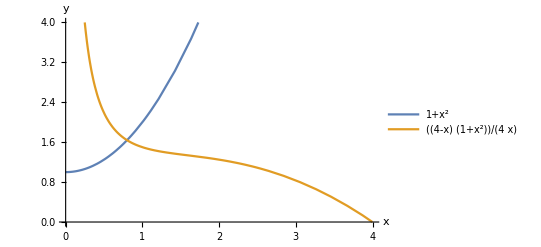

```mathematica
p1=Plot[{1+x^2,(4-x)*(1+x^2)/(4*x)},{x,0,10},PlotRange->{{0,4},{0,4}},AxesLabel->{x,y},PlotLegends->"Expressions"]
```

```mathematica
Export["null-chemo.jpg",p1,CompressionLevel->0]
```

null-chemo.jpg

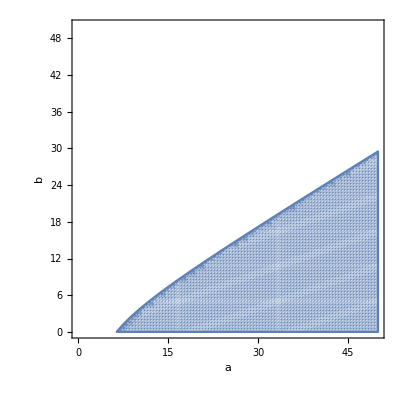

```mathematica
r1=RegionPlot[b<(3*a/5)-25/a,{a,0,50},{b,0,50},FrameLabel->{a,b},PlotPoints->100]
```

```mathematica
Export["paramsp-chemo.jpg",r1,CompressionLevel->0]
```

paramsp-chemo.jpg

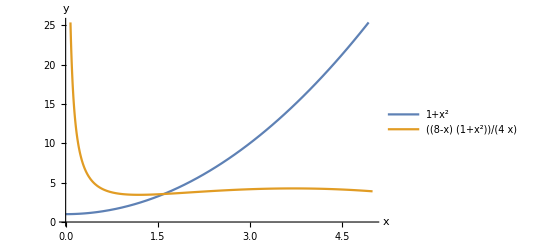

```mathematica
Plot[{1+x^2,(8-x)*(1+x^2)/(4*x)},{x,0,5},AxesLabel->{x,y},PlotLegends->"Expressions"]
```

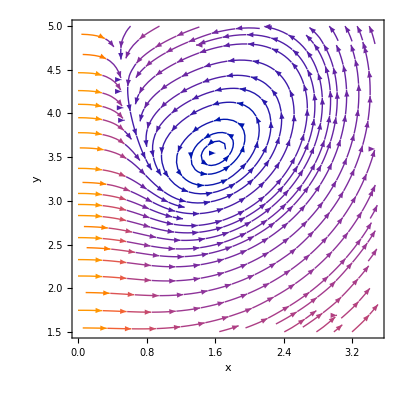

```mathematica
sp1=StreamPlot[{8-x-4*x*y/(1+x^2),1*x*(1-y/(1+x^2))},{x,0,3.5},{y,1.5,5},FrameLabel->{x,y}]
```

```mathematica
scyc=NDSolve[{x'[t]==8-x[t]-4*x[t]*y[t]/(1+x[t]^2),y'[t]==1*x[t]*(1-y[t]/(1+x[t]^2)),x[0]==5,y[0]==20},{x,y},{t,0,500}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

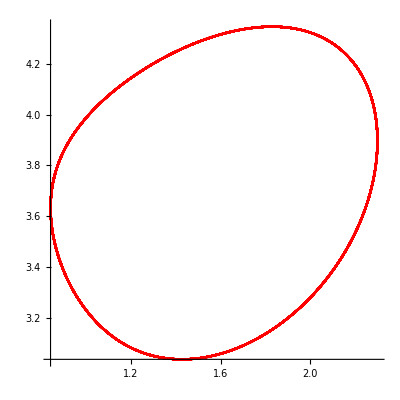

```mathematica
pp1=ParametricPlot[Evaluate[{x[t],y[t]}/.scyc],{t,400,500},AspectRatio->1,PlotStyle->Red]
```

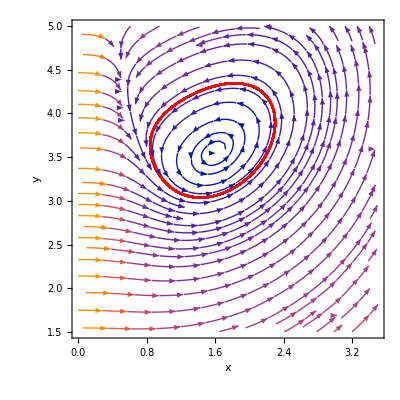

```mathematica
cyc1=Show[sp1,pp1]
```

```mathematica
Export["cycle-chemo.jpg",cyc1,CompressionLevel->0]
```

cycle-chemo.jpg

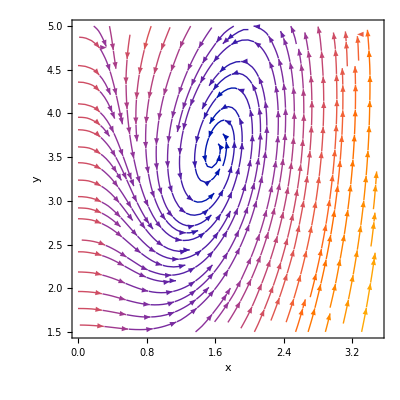

```mathematica
sp2=StreamPlot[{8-x-4*x*y/(1+x^2),5*x*(1-y/(1+x^2))},{x,0,3.5},{y,1.5,5},FrameLabel->{x,y}]
```

```mathematica
Export["stabp-chemo.jpg",sp2,CompressionLevel->0]
```

stabp-chemo.jpg

```mathematica
Manipulate[StreamPlot[{8-x-4*x*y/(1+x^2),b*x*(1-y/(1+x^2))},{x,0,3.5},{y,1.5,5},FrameLabel->{x,y}],{b,0,3.35}]
```

```mathematica
N[2*((3*a/5)-25/a)/.{a->8}]
```

3.35